## 初始化

```mathematica
Clear["Global`*"]
ClearAll["Global`*"]
mydir="/home/bosonicli/Documents/MehrWert/currency";
SetDirectory[mydir];
```

## 框架

```mathematica
(* Custom barchart pattern that stacks association. Association in, pie chart out *)
barChartAssocStacked[assocList_]:=Module[{},
BarChart[assocList,
ChartLayout->"Stacked",ChartStyle->"Pastel",ChartLegends->Keys[assocList[[1]]],ImageSize->Large
]
];

periodRepay[qrp_:0,prp_:0,irp_:0]:=Module[{},
Association["Quota"->qrp,"Principal"->prp,"Interest"->irp]
]

periodResidule[qrd_:0,prd_:0,ird_:0]:=Module[{},
Association["Quota"->qrd,"Principal"->prd,"Interest"->ird]
]

periodSchedule[pl_:1,rp_:periodRepay[],rd_:periodResidule[]]:=Module[{},
Association["PeriodRemain"->pl,"Repay"->rp,"Residule"->rd]
];

periodTest=periodSchedule[];

rescalePeriodSchedule[periodScheduleRaw_,multiplier_:1]:=Module[{},
periodSchedule[
periodScheduleRaw["PeriodRemain"],
periodScheduleRaw["Repay"]*multiplier,
periodScheduleRaw["Residule"]*multiplier
]
]

scheduleRawETP[periods_,interestRatePeriod_]:=Module[
{
periodRemain=0,principalResiduleRescalar=1,
periodScheduleNext=periodSchedule[],
periodSchedulePresent=periodSchedule[],
periodScheduleLast=periodSchedule[],
periodScheduleFirst=periodSchedule[],
totalSchedule={},
sumSchedule
},
Do[
periodSchedulePresent=periodSchedule[];
periodSchedulePresent["PeriodRemain"]=periodRemain;
periodSchedulePresent["Residule"]["Principal"]=1+(periodScheduleNext["Residule"]["Principal"])/(1+interestRatePeriod);
periodSchedulePresent["Repay"]["Principal"]=periodSchedulePresent["Residule"]["Principal"]-periodScheduleNext["Residule"]["Principal"];
periodSchedulePresent["Repay"]["Interest"]=periodSchedulePresent["Residule"]["Principal"]*interestRatePeriod;
periodSchedulePresent["Repay"]["Quota"]=periodSchedulePresent["Repay"]["Principal"]+periodSchedulePresent["Repay"]["Interest"];
periodSchedulePresent["Residule"]["Quota"]=periodSchedulePresent["Repay"]["Quota"]+periodScheduleNext["Residule"]["Quota"];
periodSchedulePresent["Residule"]["Interest"]=periodSchedulePresent["Residule"]["Quota"]-periodSchedulePresent["Residule"]["Principal"];
periodScheduleNext=periodSchedulePresent;
totalSchedule=Prepend[totalSchedule,periodSchedulePresent];
If[periodRemain==1,periodScheduleLast=periodSchedulePresent];
If[periodRemain==periods,periodScheduleFirst=periodSchedulePresent];
periodRemain=periodRemain+1
,{periodRemain,1,periods}
];
sumSchedule=Association[
"Periods"->periods,
"Quota"->periodScheduleFirst["Residule"]["Quota"],
"Principal"->periodScheduleFirst["Residule"]["Principal"],
"Interest"->periodScheduleFirst["Residule"]["Interest"],
"PeriodQuota"->periodScheduleFirst["Repay"]["Quota"],
"FirstInterest"->periodScheduleFirst["Repay"]["Interest"]
];
Association[
"TotalSchedule"->totalSchedule,
"PeriodScheduleFirst"->periodScheduleFirst,
"PeriodScheduleLast"->periodScheduleLast,
"SumSchedule"->sumSchedule
]
]

scheduleRawEPP[periods_,interestRatePeriod_]:=Module[
{
principalResiduleRescalar=1,periodRemain=0,
periodScheduleNext=periodSchedule[],
periodSchedulePresent=periodSchedule[],
periodScheduleLast=periodSchedule[],
periodScheduleFirst=periodSchedule[],
totalSchedule={},
sumSchedule
},
Do[
periodSchedulePresent=periodSchedule[
periodRemain,
periodRepay[
1+interestRatePeriod*periodRemain,
1,
interestRatePeriod*periodRemain
]
,
periodResidule[
periodRemain+interestRatePeriod*(periodRemain*(periodRemain+1))/2,
periodRemain,
interestRatePeriod*(periodRemain*(periodRemain+1))/2
]
];
totalSchedule=Prepend[totalSchedule,periodSchedulePresent];
If[periodRemain==1,periodScheduleLast=periodSchedulePresent];
If[periodRemain==periods,periodScheduleFirst=periodSchedulePresent];
periodRemain=periodRemain+1
,{periodRemain,1,periods}
];
sumSchedule=Association[
"Periods"->periods,
"Quota"->periodScheduleFirst["Residule"]["Quota"],
"Principal"->periodScheduleFirst["Residule"]["Principal"],
"Interest"->periodScheduleFirst["Residule"]["Interest"],
"PeriodPrincipal"->periodScheduleLast["Repay"]["Principal"],
"MaxInterest"->periodScheduleFirst["Repay"]["Interest"]
];
Association[
"TotalSchedule"->totalSchedule,
"PeriodScheduleFirst"->periodScheduleFirst,
"PeriodScheduleLast"->periodScheduleLast,
"SumSchedule"->sumSchedule
]
]

repaySchedule[periods_,interestRatePeriod_,totalPrincipal_:1,RepayPlan_:"ETP"]:=Module[
{
principalResiduleRescalar=1,
scheduleRaw,
totalSchedule,
uniformSchedule,
sumSchedule,
scheduleIllustrateRepay,
scheduleIllustrateResidule
},
scheduleRaw=Switch[
RepayPlan,
"ETP",
scheduleRawETP[periods,interestRatePeriod],
"EPP",
scheduleRawEPP[periods,interestRatePeriod]
];
principalResiduleRescalar=1/(scheduleRaw["SumSchedule"]["Principal"]);
totalSchedule=rescalePeriodSchedule[#,principalResiduleRescalar]&/@scheduleRaw["TotalSchedule"];
totalSchedule=rescalePeriodSchedule[#,totalPrincipal]&/@totalSchedule;
scheduleIllustrateRepay=Association[
"Interest"->#["Repay"]["Interest"],
"Principal"->#["Repay"]["Principal"]
]&/@totalSchedule;
scheduleIllustrateResidule=#["Residule"]["Principal"]&/@totalSchedule;
uniformSchedule=scheduleRaw["SumSchedule"]*principalResiduleRescalar;
uniformSchedule["Periods"]=periods;
sumSchedule=scheduleRaw["SumSchedule"]*principalResiduleRescalar*totalPrincipal;
sumSchedule["Periods"]=periods;
Association[
"SumSchedule"->sumSchedule,
"UniformSchedule"->uniformSchedule,
"TotalSchedule"->totalSchedule,
"ScheduleIllustrateRepay"->scheduleIllustrateRepay,
"ScheduleIllustrateResidule"->scheduleIllustrateResidule
]
];
```

## 面板

<|SumSchedule→<|Periods→120,Quota→33.3062,Principal→25.,Interest→8.30615,PeriodQuota→0.277551,FirstInterest→0.125|>,UniformSchedule→<|Periods→120,Quota→1.33225,Principal→1.,Interest→0.332246,PeriodQuota→0.0111021,FirstInterest→0.005|>,TotalSchedule→{<|PeriodRemain→120,Repay→<|Quota→0.277551,Principal→0.152551,Interest→0.125|>,Residule→<|Quota→33.3062,Principal→25.,Interest→8.30615|>|>,<|PeriodRemain→119,Repay→<|Quota→0.277551,Principal→0.153314,Interest→0.124237|>,Residule→<|Quota→33.0286,Principal→24.8474,Interest→8.18115|>|>,<|PeriodRemain→118,Repay→<|Quota→0.277551,Principal→0.154081,Interest→0.123471|>,Residule→<|Quota→32.751,Principal→24.6941,Interest→8.05691|>|>,<|PeriodRemain→117,Repay→<|Quota→0.277551,Principal→0.154851,Interest→0.1227|>,Residule→<|Quota→32.4735,Principal→24.5401,Interest→7.93344|>|>,<|PeriodRemain→116,Repay→<|Quota→0.277551,Principal→0.155625,Interest→0.121926|>,Residule→<|Quota→32.1959,Principal→24.3852,Interest→7.81074|>|>,<|PeriodRemain→115,Repay→<|Quota→0.277551,Principal→0.156403,Interest→0.121148|>,Residule→<|Quota→31.9184,Principal→24.2296,Interest→7.68882|>|>,<|PeriodRemain→114,Repay→<|Quota→0.277551,Principal→0.157185,Interest→0.120366|>,Residule→<|Quota→31.6408,Principal→24.0732,Interest→7.56767|>|>,<|PeriodRemain→113,Repay→<|Quota→0.277551,Principal→0.157971,Interest→0.11958|>,Residule→<|Quota→31.3633,Principal→23.916,Interest→7.4473|>|>,<|PeriodRemain→112,Repay→<|Quota→0.277551,Principal→0.158761,Interest→0.11879|>,Residule→<|Quota→31.0857,Principal→23.758,Interest→7.32772|>|>,<|PeriodRemain→111,Repay→<|Quota→0.277551,Principal→0.159555,Interest→0.117996|>,Residule→<|Quota→30.8082,Principal→23.5993,Interest→7.20893|>|>,<|PeriodRemain→110,Repay→<|Quota→0.277551,Principal→0.160353,Interest→0.117199|>,Residule→<|Quota→30.5306,Principal→23.4397,Interest→7.09094|>|>,<|PeriodRemain→109,Repay→<|Quota→0.277551,Principal→0.161155,Interest→0.116397|>,Residule→<|Quota→30.2531,Principal→23.2793,Interest→6.97374|>|>,<|PeriodRemain→108,Repay→<|Quota→0.277551,Principal→0.16196,Interest→0.115591|>,Residule→<|Quota→29.9755,Principal→23.1182,Interest→6.85734|>|>,<|PeriodRemain→107,Repay→<|Quota→0.277551,Principal→0.16277,Interest→0.114781|>,Residule→<|Quota→29.698,Principal→22.9562,Interest→6.74175|>|>,<|PeriodRemain→106,Repay→<|Quota→0.277551,Principal→0.163584,Interest→0.113967|>,Residule→<|Quota→29.4204,Principal→22.7935,Interest→6.62697|>|>,<|PeriodRemain→105,Repay→<|Quota→0.277551,Principal→0.164402,Interest→0.113149|>,Residule→<|Quota→29.1429,Principal→22.6299,Interest→6.513|>|>,<|PeriodRemain→104,Repay→<|Quota→0.277551,Principal→0.165224,Interest→0.112327|>,Residule→<|Quota→28.8653,Principal→22.4655,Interest→6.39985|>|>,<|PeriodRemain→103,Repay→<|Quota→0.277551,Principal→0.16605,Interest→0.111501|>,Residule→<|Quota→28.5878,Principal→22.3003,Interest→6.28752|>|>,<|PeriodRemain→102,Repay→<|Quota→0.277551,Principal→0.16688,Interest→0.110671|>,Residule→<|Quota→28.3102,Principal→22.1342,Interest→6.17602|>|>,<|PeriodRemain→101,Repay→<|Quota→0.277551,Principal→0.167715,Interest→0.109837|>,Residule→<|Quota→28.0327,Principal→21.9673,Interest→6.06535|>|>,<|PeriodRemain→100,Repay→<|Quota→0.277551,Principal→0.168553,Interest→0.108998|>,Residule→<|Quota→27.7551,Principal→21.7996,Interest→5.95552|>|>,<|PeriodRemain→99,Repay→<|Quota→0.277551,Principal→0.169396,Interest→0.108155|>,Residule→<|Quota→27.4776,Principal→21.6311,Interest→5.84652|>|>,<|PeriodRemain→98,Repay→<|Quota→0.277551,Principal→0.170243,Interest→0.107308|>,Residule→<|Quota→27.2,Principal→21.4617,Interest→5.73836|>|>,<|PeriodRemain→97,Repay→<|Quota→0.277551,Principal→0.171094,Interest→0.106457|>,Residule→<|Quota→26.9225,Principal→21.2914,Interest→5.63105|>|>,<|PeriodRemain→96,Repay→<|Quota→0.277551,Principal→0.17195,Interest→0.105602|>,Residule→<|Quota→26.6449,Principal→21.1203,Interest→5.5246|>|>,<|PeriodRemain→95,Repay→<|Quota→0.277551,Principal→0.172809,Interest→0.104742|>,Residule→<|Quota→26.3674,Principal→20.9484,Interest→5.419|>|>,<|PeriodRemain→94,Repay→<|Quota→0.277551,Principal→0.173673,Interest→0.103878|>,Residule→<|Quota→26.0898,Principal→20.7756,Interest→5.31425|>|>,<|PeriodRemain→93,Repay→<|Quota→0.277551,Principal→0.174542,Interest→0.103009|>,Residule→<|Quota→25.8123,Principal→20.6019,Interest→5.21038|>|>,<|PeriodRemain→92,Repay→<|Quota→0.277551,Principal→0.175415,Interest→0.102137|>,Residule→<|Quota→25.5347,Principal→20.4273,Interest→5.10737|>|>,<|PeriodRemain→91,Repay→<|Quota→0.277551,Principal→0.176292,Interest→0.10126|>,Residule→<|Quota→25.2572,Principal→20.2519,Interest→5.00523|>|>,<|PeriodRemain→90,Repay→<|Quota→0.277551,Principal→0.177173,Interest→0.100378|>,Residule→<|Quota→24.9796,Principal→20.0756,Interest→4.90397|>|>,<|PeriodRemain→89,Repay→<|Quota→0.277551,Principal→0.178059,Interest→0.0994923|>,Residule→<|Quota→24.7021,Principal→19.8985,Interest→4.80359|>|>,<|PeriodRemain→88,Repay→<|Quota→0.277551,Principal→0.178949,Interest→0.0986021|>,Residule→<|Quota→24.4245,Principal→19.7204,Interest→4.7041|>|>,<|PeriodRemain→87,Repay→<|Quota→0.277551,Principal→0.179844,Interest→0.0977073|>,Residule→<|Quota→24.147,Principal→19.5415,Interest→4.6055|>|>,<|PeriodRemain→86,Repay→<|Quota→0.277551,Principal→0.180743,Interest→0.0968081|>,Residule→<|Quota→23.8694,Principal→19.3616,Interest→4.50779|>|>,<|PeriodRemain→85,Repay→<|Quota→0.277551,Principal→0.181647,Interest→0.0959044|>,Residule→<|Quota→23.5919,Principal→19.1809,Interest→4.41098|>|>,<|PeriodRemain→84,Repay→<|Quota→0.277551,Principal→0.182555,Interest→0.0949961|>,Residule→<|Quota→23.3143,Principal→18.9992,Interest→4.31508|>|>,<|PeriodRemain→83,Repay→<|Quota→0.277551,Principal→0.183468,Interest→0.0940834|>,Residule→<|Quota→23.0368,Principal→18.8167,Interest→4.22008|>|>,<|PeriodRemain→82,Repay→<|Quota→0.277551,Principal→0.184385,Interest→0.093166|>,Residule→<|Quota→22.7592,Principal→18.6332,Interest→4.126|>|>,<|PeriodRemain→81,Repay→<|Quota→0.277551,Principal→0.185307,Interest→0.0922441|>,Residule→<|Quota→22.4817,Principal→18.4488,Interest→4.03283|>|>,<|PeriodRemain→80,Repay→<|Quota→0.277551,Principal→0.186234,Interest→0.0913176|>,Residule→<|Quota→22.2041,Principal→18.2635,Interest→3.94059|>|>,<|PeriodRemain→79,Repay→<|Quota→0.277551,Principal→0.187165,Interest→0.0903864|>,Residule→<|Quota→21.9265,Principal→18.0773,Interest→3.84927|>|>,<|PeriodRemain→78,Repay→<|Quota→0.277551,Principal→0.188101,Interest→0.0894506|>,Residule→<|Quota→21.649,Principal→17.8901,Interest→3.75888|>|>,<|PeriodRemain→77,Repay→<|Quota→0.277551,Principal→0.189041,Interest→0.0885101|>,Residule→<|Quota→21.3714,Principal→17.702,Interest→3.66943|>|>,<|PeriodRemain→76,Repay→<|Quota→0.277551,Principal→0.189986,Interest→0.0875649|>,Residule→<|Quota→21.0939,Principal→17.513,Interest→3.58092|>|>,<|PeriodRemain→75,Repay→<|Quota→0.277551,Principal→0.190936,Interest→0.0866149|>,Residule→<|Quota→20.8163,Principal→17.323,Interest→3.49336|>|>,<|PeriodRemain→74,Repay→<|Quota→0.277551,Principal→0.191891,Interest→0.0856602|>,Residule→<|Quota→20.5388,Principal→17.132,Interest→3.40674|>|>,<|PeriodRemain→73,Repay→<|Quota→0.277551,Principal→0.19285,Interest→0.0847008|>,Residule→<|Quota→20.2612,Principal→16.9402,Interest→3.32108|>|>,<|PeriodRemain→72,Repay→<|Quota→0.277551,Principal→0.193815,Interest→0.0837365|>,Residule→<|Quota→19.9837,Principal→16.7473,Interest→3.23638|>|>,<|PeriodRemain→71,Repay→<|Quota→0.277551,Principal→0.194784,Interest→0.0827675|>,Residule→<|Quota→19.7061,Principal→16.5535,Interest→3.15265|>|>,<|PeriodRemain→70,Repay→<|Quota→0.277551,Principal→0.195758,Interest→0.0817935|>,Residule→<|Quota→19.4286,Principal→16.3587,Interest→3.06988|>|>,<|PeriodRemain→69,Repay→<|Quota→0.277551,Principal→0.196736,Interest→0.0808148|>,Residule→<|Quota→19.151,Principal→16.163,Interest→2.98808|>|>,<|PeriodRemain→68,Repay→<|Quota→0.277551,Principal→0.19772,Interest→0.0798311|>,Residule→<|Quota→18.8735,Principal→15.9662,Interest→2.90727|>|>,<|PeriodRemain→67,Repay→<|Quota→0.277551,Principal→0.198709,Interest→0.0788425|>,Residule→<|Quota→18.5959,Principal→15.7685,Interest→2.82744|>|>,<|PeriodRemain→66,Repay→<|Quota→0.277551,Principal→0.199702,Interest→0.0778489|>,Residule→<|Quota→18.3184,Principal→15.5698,Interest→2.7486|>|>,<|PeriodRemain→65,Repay→<|Quota→0.277551,Principal→0.200701,Interest→0.0768504|>,Residule→<|Quota→18.0408,Principal→15.3701,Interest→2.67075|>|>,<|PeriodRemain→64,Repay→<|Quota→0.277551,Principal→0.201704,Interest→0.0758469|>,Residule→<|Quota→17.7633,Principal→15.1694,Interest→2.5939|>|>,<|PeriodRemain→63,Repay→<|Quota→0.277551,Principal→0.202713,Interest→0.0748384|>,Residule→<|Quota→17.4857,Principal→14.9677,Interest→2.51805|>|>,<|PeriodRemain→62,Repay→<|Quota→0.277551,Principal→0.203726,Interest→0.0738248|>,Residule→<|Quota→17.2082,Principal→14.765,Interest→2.44321|>|>,<|PeriodRemain→61,Repay→<|Quota→0.277551,Principal→0.204745,Interest→0.0728062|>,Residule→<|Quota→16.9306,Principal→14.5612,Interest→2.36939|>|>,<|PeriodRemain→60,Repay→<|Quota→0.277551,Principal→0.205769,Interest→0.0717825|>,Residule→<|Quota→16.6531,Principal→14.3565,Interest→2.29658|>|>,<|PeriodRemain→59,Repay→<|Quota→0.277551,Principal→0.206798,Interest→0.0707536|>,Residule→<|Quota→16.3755,Principal→14.1507,Interest→2.2248|>|>,<|PeriodRemain→58,Repay→<|Quota→0.277551,Principal→0.207832,Interest→0.0697196|>,Residule→<|Quota→16.098,Principal→13.9439,Interest→2.15404|>|>,<|PeriodRemain→57,Repay→<|Quota→0.277551,Principal→0.208871,Interest→0.0686805|>,Residule→<|Quota→15.8204,Principal→13.7361,Interest→2.08433|>|>,<|PeriodRemain→56,Repay→<|Quota→0.277551,Principal→0.209915,Interest→0.0676361|>,Residule→<|Quota→15.5429,Principal→13.5272,Interest→2.01564|>|>,<|PeriodRemain→55,Repay→<|Quota→0.277551,Principal→0.210965,Interest→0.0665866|>,Residule→<|Quota→15.2653,Principal→13.3173,Interest→1.94801|>|>,<|PeriodRemain→54,Repay→<|Quota→0.277551,Principal→0.21202,Interest→0.0655317|>,Residule→<|Quota→14.9878,Principal→13.1063,Interest→1.88142|>|>,<|PeriodRemain→53,Repay→<|Quota→0.277551,Principal→0.21308,Interest→0.0644716|>,Residule→<|Quota→14.7102,Principal→12.8943,Interest→1.81589|>|>,<|PeriodRemain→52,Repay→<|Quota→0.277551,Principal→0.214145,Interest→0.0634062|>,Residule→<|Quota→14.4327,Principal→12.6812,Interest→1.75142|>|>,<|PeriodRemain→51,Repay→<|Quota→0.277551,Principal→0.215216,Interest→0.0623355|>,Residule→<|Quota→14.1551,Principal→12.4671,Interest→1.68801|>|>,<|PeriodRemain→50,Repay→<|Quota→0.277551,Principal→0.216292,Interest→0.0612594|>,Residule→<|Quota→13.8776,Principal→12.2519,Interest→1.62568|>|>,<|PeriodRemain→49,Repay→<|Quota→0.277551,Principal→0.217373,Interest→0.060178|>,Residule→<|Quota→13.6,Principal→12.0356,Interest→1.56442|>|>,<|PeriodRemain→48,Repay→<|Quota→0.277551,Principal→0.21846,Interest→0.0590911|>,Residule→<|Quota→13.3225,Principal→11.8182,Interest→1.50424|>|>,<|PeriodRemain→47,Repay→<|Quota→0.277551,Principal→0.219552,Interest→0.0579988|>,Residule→<|Quota→13.0449,Principal→11.5998,Interest→1.44515|>|>,<|PeriodRemain→46,Repay→<|Quota→0.277551,Principal→0.22065,Interest→0.056901|>,Residule→<|Quota→12.7674,Principal→11.3802,Interest→1.38715|>|>,<|PeriodRemain→45,Repay→<|Quota→0.277551,Principal→0.221753,Interest→0.0557978|>,Residule→<|Quota→12.4898,Principal→11.1596,Interest→1.33025|>|>,<|PeriodRemain→44,Repay→<|Quota→0.277551,Principal→0.222862,Interest→0.054689|>,Residule→<|Quota→12.2123,Principal→10.9378,Interest→1.27445|>|>,<|PeriodRemain→43,Repay→<|Quota→0.277551,Principal→0.223977,Interest→0.0535747|>,Residule→<|Quota→11.9347,Principal→10.7149,Interest→1.21976|>|>,<|PeriodRemain→42,Repay→<|Quota→0.277551,Principal→0.225096,Interest→0.0524548|>,Residule→<|Quota→11.6572,Principal→10.491,Interest→1.16619|>|>,<|PeriodRemain→41,Repay→<|Quota→0.277551,Principal→0.226222,Interest→0.0513293|>,Residule→<|Quota→11.3796,Principal→10.2659,Interest→1.11373|>|>,<|PeriodRemain→40,Repay→<|Quota→0.277551,Principal→0.227353,Interest→0.0501982|>,Residule→<|Quota→11.1021,Principal→10.0396,Interest→1.0624|>|>,<|PeriodRemain→39,Repay→<|Quota→0.277551,Principal→0.22849,Interest→0.0490615|>,Residule→<|Quota→10.8245,Principal→9.81229,Interest→1.0122|>|>,<|PeriodRemain→38,Repay→<|Quota→0.277551,Principal→0.229632,Interest→0.047919|>,Residule→<|Quota→10.5469,Principal→9.5838,Interest→0.963143|>|>,<|PeriodRemain→37,Repay→<|Quota→0.277551,Principal→0.23078,Interest→0.0467709|>,Residule→<|Quota→10.2694,Principal→9.35417,Interest→0.915224|>|>,<|PeriodRemain→36,Repay→<|Quota→0.277551,Principal→0.231934,Interest→0.045617|>,Residule→<|Quota→9.99185,Principal→9.12339,Interest→0.868453|>|>,<|PeriodRemain→35,Repay→<|Quota→0.277551,Principal→0.233094,Interest→0.0444573|>,Residule→<|Quota→9.71429,Principal→8.89146,Interest→0.822836|>|>,<|PeriodRemain→34,Repay→<|Quota→0.277551,Principal→0.234259,Interest→0.0432918|>,Residule→<|Quota→9.43674,Principal→8.65836,Interest→0.778379|>|>,<|PeriodRemain→33,Repay→<|Quota→0.277551,Principal→0.235431,Interest→0.0421205|>,Residule→<|Quota→9.15919,Principal→8.4241,Interest→0.735087|>|>,<|PeriodRemain→32,Repay→<|Quota→0.277551,Principal→0.236608,Interest→0.0409434|>,Residule→<|Quota→8.88164,Principal→8.18867,Interest→0.692967|>|>,<|PeriodRemain→31,Repay→<|Quota→0.277551,Principal→0.237791,Interest→0.0397603|>,Residule→<|Quota→8.60409,Principal→7.95207,Interest→0.652023|>|>,<|PeriodRemain→30,Repay→<|Quota→0.277551,Principal→0.23898,Interest→0.0385714|>,Residule→<|Quota→8.32654,Principal→7.71427,Interest→0.612263|>|>,<|PeriodRemain→29,Repay→<|Quota→0.277551,Principal→0.240175,Interest→0.0373765|>,Residule→<|Quota→8.04899,Principal→7.47529,Interest→0.573692|>|>,<|PeriodRemain→28,Repay→<|Quota→0.277551,Principal→0.241376,Interest→0.0361756|>,Residule→<|Quota→7.77144,Principal→7.23512,Interest→0.536315|>|>,<|PeriodRemain→27,Repay→<|Quota→0.277551,Principal→0.242583,Interest→0.0349687|>,Residule→<|Quota→7.49388,Principal→6.99374,Interest→0.50014|>|>,<|PeriodRemain→26,Repay→<|Quota→0.277551,Principal→0.243795,Interest→0.0337558|>,Residule→<|Quota→7.21633,Principal→6.75116,Interest→0.465171|>|>,<|PeriodRemain→25,Repay→<|Quota→0.277551,Principal→0.245014,Interest→0.0325368|>,Residule→<|Quota→6.93878,Principal→6.50737,Interest→0.431415|>|>,<|PeriodRemain→24,Repay→<|Quota→0.277551,Principal→0.246239,Interest→0.0313118|>,Residule→<|Quota→6.66123,Principal→6.26235,Interest→0.398878|>|>,<|PeriodRemain→23,Repay→<|Quota→0.277551,Principal→0.247471,Interest→0.0300806|>,Residule→<|Quota→6.38368,Principal→6.01611,Interest→0.367567|>|>,<|PeriodRemain→22,Repay→<|Quota→0.277551,Principal→0.248708,Interest→0.0288432|>,Residule→<|Quota→6.10613,Principal→5.76864,Interest→0.337486|>|>,<|PeriodRemain→21,Repay→<|Quota→0.277551,Principal→0.249952,Interest→0.0275997|>,Residule→<|Quota→5.82858,Principal→5.51993,Interest→0.308643|>|>,<|PeriodRemain→20,Repay→<|Quota→0.277551,Principal→0.251201,Interest→0.0263499|>,Residule→<|Quota→5.55103,Principal→5.26998,Interest→0.281043|>|>,<|PeriodRemain→19,Repay→<|Quota→0.277551,Principal→0.252457,Interest→0.0250939|>,Residule→<|Quota→5.27347,Principal→5.01878,Interest→0.254693|>|>,<|PeriodRemain→18,Repay→<|Quota→0.277551,Principal→0.25372,Interest→0.0238316|>,Residule→<|Quota→4.99592,Principal→4.76632,Interest→0.229599|>|>,<|PeriodRemain→17,Repay→<|Quota→0.277551,Principal→0.254988,Interest→0.022563|>,Residule→<|Quota→4.71837,Principal→4.5126,Interest→0.205768|>|>,<|PeriodRemain→16,Repay→<|Quota→0.277551,Principal→0.256263,Interest→0.0212881|>,Residule→<|Quota→4.44082,Principal→4.25762,Interest→0.183205|>|>,<|PeriodRemain→15,Repay→<|Quota→0.277551,Principal→0.257544,Interest→0.0200068|>,Residule→<|Quota→4.16327,Principal→4.00135,Interest→0.161917|>|>,<|PeriodRemain→14,Repay→<|Quota→0.277551,Principal→0.258832,Interest→0.018719|>,Residule→<|Quota→3.88572,Principal→3.74381,Interest→0.14191|>|>,<|PeriodRemain→13,Repay→<|Quota→0.277551,Principal→0.260126,Interest→0.0174249|>,Residule→<|Quota→3.60817,Principal→3.48498,Interest→0.123191|>|>,<|PeriodRemain→12,Repay→<|Quota→0.277551,Principal→0.261427,Interest→0.0161242|>,Residule→<|Quota→3.33062,Principal→3.22485,Interest→0.105766|>|>,<|PeriodRemain→11,Repay→<|Quota→0.277551,Principal→0.262734,Interest→0.0148171|>,Residule→<|Quota→3.05306,Principal→2.96342,Interest→0.0896416|>|>,<|PeriodRemain→10,Repay→<|Quota→0.277551,Principal→0.264048,Interest→0.0135034|>,Residule→<|Quota→2.77551,Principal→2.70069,Interest→0.0748245|>|>,<|PeriodRemain→9,Repay→<|Quota→0.277551,Principal→0.265368,Interest→0.0121832|>,Residule→<|Quota→2.49796,Principal→2.43664,Interest→0.0613211|>|>,<|PeriodRemain→8,Repay→<|Quota→0.277551,Principal→0.266695,Interest→0.0108564|>,Residule→<|Quota→2.22041,Principal→2.17127,Interest→0.0491379|>|>,<|PeriodRemain→7,Repay→<|Quota→0.277551,Principal→0.268028,Interest→0.00952289|>,Residule→<|Quota→1.94286,Principal→1.90458,Interest→0.0382815|>|>,<|PeriodRemain→6,Repay→<|Quota→0.277551,Principal→0.269369,Interest→0.00818274|>,Residule→<|Quota→1.66531,Principal→1.63655,Interest→0.0287586|>|>,<|PeriodRemain→5,Repay→<|Quota→0.277551,Principal→0.270715,Interest→0.0068359|>,Residule→<|Quota→1.38776,Principal→1.36718,Interest→0.0205759|>|>,<|PeriodRemain→4,Repay→<|Quota→0.277551,Principal→0.272069,Interest→0.00548233|>,Residule→<|Quota→1.11021,Principal→1.09647,Interest→0.01374|>|>,<|PeriodRemain→3,Repay→<|Quota→0.277551,Principal→0.273429,Interest→0.00412198|>,Residule→<|Quota→0.832654,Principal→0.824396,Interest→0.00825767|>|>,<|PeriodRemain→2,Repay→<|Quota→0.277551,Principal→0.274796,Interest→0.00275483|>,Residule→<|Quota→0.555103,Principal→0.550967,Interest→0.00413569|>|>,<|PeriodRemain→1,Repay→<|Quota→0.277551,Principal→0.27617,Interest→0.00138085|>,Residule→<|Quota→0.277551,Principal→0.27617,Interest→0.00138085|>|>},ScheduleIllustrateRepay→{<|Interest→0.125,Principal→0.152551|>,<|Interest→0.124237,Principal→0.153314|>,<|Interest→0.123471,Principal→0.154081|>,<|Interest→0.1227,Principal→0.154851|>,<|Interest→0.121926,Principal→0.155625|>,<|Interest→0.121148,Principal→0.156403|>,<|Interest→0.120366,Principal→0.157185|>,<|Interest→0.11958,Principal→0.157971|>,<|Interest→0.11879,Principal→0.158761|>,<|Interest→0.117996,Principal→0.159555|>,<|Interest→0.117199,Principal→0.160353|>,<|Interest→0.116397,Principal→0.161155|>,<|Interest→0.115591,Principal→0.16196|>,<|Interest→0.114781,Principal→0.16277|>,<|Interest→0.113967,Principal→0.163584|>,<|Interest→0.113149,Principal→0.164402|>,<|Interest→0.112327,Principal→0.165224|>,<|Interest→0.111501,Principal→0.16605|>,<|Interest→0.110671,Principal→0.16688|>,<|Interest→0.109837,Principal→0.167715|>,<|Interest→0.108998,Principal→0.168553|>,<|Interest→0.108155,Principal→0.169396|>,<|Interest→0.107308,Principal→0.170243|>,<|Interest→0.106457,Principal→0.171094|>,<|Interest→0.105602,Principal→0.17195|>,<|Interest→0.104742,Principal→0.172809|>,<|Interest→0.103878,Principal→0.173673|>,<|Interest→0.103009,Principal→0.174542|>,<|Interest→0.102137,Principal→0.175415|>,<|Interest→0.10126,Principal→0.176292|>,<|Interest→0.100378,Principal→0.177173|>,<|Interest→0.0994923,Principal→0.178059|>,<|Interest→0.0986021,Principal→0.178949|>,<|Interest→0.0977073,Principal→0.179844|>,<|Interest→0.0968081,Principal→0.180743|>,<|Interest→0.0959044,Principal→0.181647|>,<|Interest→0.0949961,Principal→0.182555|>,<|Interest→0.0940834,Principal→0.183468|>,<|Interest→0.093166,Principal→0.184385|>,<|Interest→0.0922441,Principal→0.185307|>,<|Interest→0.0913176,Principal→0.186234|>,<|Interest→0.0903864,Principal→0.187165|>,<|Interest→0.0894506,Principal→0.188101|>,<|Interest→0.0885101,Principal→0.189041|>,<|Interest→0.0875649,Principal→0.189986|>,<|Interest→0.0866149,Principal→0.190936|>,<|Interest→0.0856602,Principal→0.191891|>,<|Interest→0.0847008,Principal→0.19285|>,<|Interest→0.0837365,Principal→0.193815|>,<|Interest→0.0827675,Principal→0.194784|>,<|Interest→0.0817935,Principal→0.195758|>,<|Interest→0.0808148,Principal→0.196736|>,<|Interest→0.0798311,Principal→0.19772|>,<|Interest→0.0788425,Principal→0.198709|>,<|Interest→0.0778489,Principal→0.199702|>,<|Interest→0.0768504,Principal→0.200701|>,<|Interest→0.0758469,Principal→0.201704|>,<|Interest→0.0748384,Principal→0.202713|>,<|Interest→0.0738248,Principal→0.203726|>,<|Interest→0.0728062,Principal→0.204745|>,<|Interest→0.0717825,Principal→0.205769|>,<|Interest→0.0707536,Principal→0.206798|>,<|Interest→0.0697196,Principal→0.207832|>,<|Interest→0.0686805,Principal→0.208871|>,<|Interest→0.0676361,Principal→0.209915|>,<|Interest→0.0665866,Principal→0.210965|>,<|Interest→0.0655317,Principal→0.21202|>,<|Interest→0.0644716,Principal→0.21308|>,<|Interest→0.0634062,Principal→0.214145|>,<|Interest→0.0623355,Principal→0.215216|>,<|Interest→0.0612594,Principal→0.216292|>,<|Interest→0.060178,Principal→0.217373|>,<|Interest→0.0590911,Principal→0.21846|>,<|Interest→0.0579988,Principal→0.219552|>,<|Interest→0.056901,Principal→0.22065|>,<|Interest→0.0557978,Principal→0.221753|>,<|Interest→0.054689,Principal→0.222862|>,<|Interest→0.0535747,Principal→0.223977|>,<|Interest→0.0524548,Principal→0.225096|>,<|Interest→0.0513293,Principal→0.226222|>,<|Interest→0.0501982,Principal→0.227353|>,<|Interest→0.0490615,Principal→0.22849|>,<|Interest→0.047919,Principal→0.229632|>,<|Interest→0.0467709,Principal→0.23078|>,<|Interest→0.045617,Principal→0.231934|>,<|Interest→0.0444573,Principal→0.233094|>,<|Interest→0.0432918,Principal→0.234259|>,<|Interest→0.0421205,Principal→0.235431|>,<|Interest→0.0409434,Principal→0.236608|>,<|Interest→0.0397603,Principal→0.237791|>,<|Interest→0.0385714,Principal→0.23898|>,<|Interest→0.0373765,Principal→0.240175|>,<|Interest→0.0361756,Principal→0.241376|>,<|Interest→0.0349687,Principal→0.242583|>,<|Interest→0.0337558,Principal→0.243795|>,<|Interest→0.0325368,Principal→0.245014|>,<|Interest→0.0313118,Principal→0.246239|>,<|Interest→0.0300806,Principal→0.247471|>,<|Interest→0.0288432,Principal→0.248708|>,<|Interest→0.0275997,Principal→0.249952|>,<|Interest→0.0263499,Principal→0.251201|>,<|Interest→0.0250939,Principal→0.252457|>,<|Interest→0.0238316,Principal→0.25372|>,<|Interest→0.022563,Principal→0.254988|>,<|Interest→0.0212881,Principal→0.256263|>,<|Interest→0.0200068,Principal→0.257544|>,<|Interest→0.018719,Principal→0.258832|>,<|Interest→0.0174249,Principal→0.260126|>,<|Interest→0.0161242,Principal→0.261427|>,<|Interest→0.0148171,Principal→0.262734|>,<|Interest→0.0135034,Principal→0.264048|>,<|Interest→0.0121832,Principal→0.265368|>,<|Interest→0.0108564,Principal→0.266695|>,<|Interest→0.00952289,Principal→0.268028|>,<|Interest→0.00818274,Principal→0.269369|>,<|Interest→0.0068359,Principal→0.270715|>,<|Interest→0.00548233,Principal→0.272069|>,<|Interest→0.00412198,Principal→0.273429|>,<|Interest→0.00275483,Principal→0.274796|>,<|Interest→0.00138085,Principal→0.27617|>},ScheduleIllustrateResidule→{25.,24.8474,24.6941,24.5401,24.3852,24.2296,24.0732,23.916,23.758,23.5993,23.4397,23.2793,23.1182,22.9562,22.7935,22.6299,22.4655,22.3003,22.1342,21.9673,21.7996,21.6311,21.4617,21.2914,21.1203,20.9484,20.7756,20.6019,20.4273,20.2519,20.0756,19.8985,19.7204,19.5415,19.3616,19.1809,18.9992,18.8167,18.6332,18.4488,18.2635,18.0773,17.8901,17.702,17.513,17.323,17.132,16.9402,16.7473,16.5535,16.3587,16.163,15.9662,15.7685,15.5698,15.3701,15.1694,14.9677,14.765,14.5612,14.3565,14.1507,13.9439,13.7361,13.5272,13.3173,13.1063,12.8943,12.6812,12.4671,12.2519,12.0356,11.8182,11.5998,11.3802,11.1596,10.9378,10.7149,10.491,10.2659,10.0396,9.81229,9.5838,9.35417,9.12339,8.89146,8.65836,8.4241,8.18867,7.95207,7.71427,7.47529,7.23512,6.99374,6.75116,6.50737,6.26235,6.01611,5.76864,5.51993,5.26998,5.01878,4.76632,4.5126,4.25762,4.00135,3.74381,3.48498,3.22485,2.96342,2.70069,2.43664,2.17127,1.90458,1.63655,1.36718,1.09647,0.824396,0.550967,0.27617}|>

<|Periods→120,Quota→1.33225,Principal→1.,Interest→0.332246,PeriodQuota→0.0111021,FirstInterest→0.005|>

<|Periods→120,Quota→1.3025,Principal→1,Interest→0.3025,PeriodPrincipal→1/120,MaxInterest→0.005|>

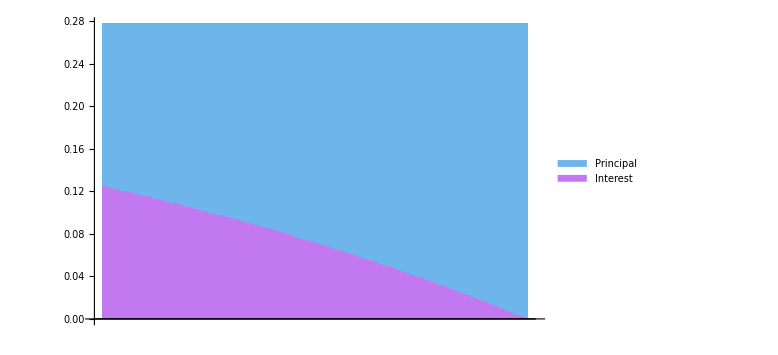

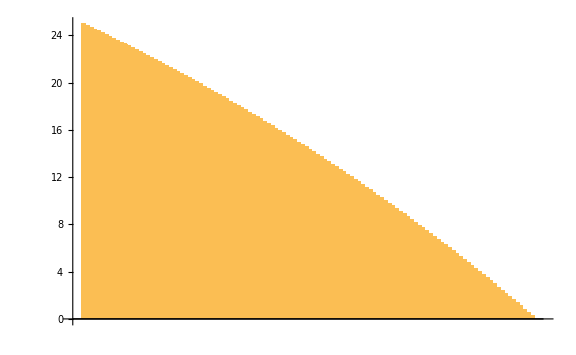

```mathematica
testRawETP=scheduleRawETP[120,0.06/12];
testRawEPP=scheduleRawEPP[120,0.06/12];

testRepay1=repaySchedule[120,0.06/12,25,"ETP"]
testRepay2=repaySchedule[120,0.06/12,25,"EPP"];

testRepay1["UniformSchedule"]
testRepay2["UniformSchedule"]

barChartAssocStacked[testRepay1["ScheduleIllustrateRepay"]]
BarChart[testRepay1["ScheduleIllustrateResidule"],ImageSize->Large]
```